```mathematica
SetDirectory[NotebookDirectory[]];
<<ErrorBarPlots`
(files=FileNames["data/*"])//TableForm
```

data\calibration2.center.csv
data\calibration2.sample.csv
data\calibration3.center.csv
data\calibration.center.csv
data\calibration.sample.csv
data\drift2.csv
data\drift3.short.csv
data\drift4.shortz.csv
data\drift.csv
data\hys.easy.1.csv
data\hys.easy.2.csv
data\hys.easy.3.csv
data\hys.easy.4.csv
data\hys.hard.1.csv
data\hys.hard.2.csv
data\hys.hard.3.csv
data\hys.hard.4.csv
data\hys.hard.5.csv
data\hys.hard.6.csv
data\hys.hard.7.csv
data\kerreinfallswinkelmessung.ods
data\kerreinfallswinkelmessungpp.ods
data\kerrwinkelmessung.ods
data\microscope
data\placeholder.txt
data\p.polar.einfallswinkel
data\s.polar.einfallswinkel
data\winkel

```mathematica
applyWithError[fct_,arg_]:=Module[{i,total,direction},
total=0;
(* calculate gauss error *)
direction=Table[0,{i,1,Length[arg]}];
For[i=1,i≤Length[arg],i++,
direction⟦i⟧=1;
total+=(((Derivative@@direction)[fct])@@arg⟦1;;,1⟧)^2*arg⟦i,2⟧^2;
direction⟦i⟧=0;
];
{fct@@arg⟦1;;,1⟧,Sqrt[total]}
]
```

## read data

```mathematica
offset[dat_,offset_]:={#⟦1⟧,#⟦2⟧+offset}&/@dat;
str=OpenRead[files⟦2⟧];
datCali=ReadList[str,{Number,Number}];
str=OpenRead[files⟦1⟧];
datCaliCenter=ReadList[str,{Number,Number}];

str=OpenRead[files⟦10⟧];
datEasy1=ReadList[str,{Number,Number}]~offset~1.648;
str=OpenRead[files⟦11⟧];
datEasy2=ReadList[str,{Number,Number}]~offset~1.648;
str=OpenRead[files⟦12⟧];
datEasy3=ReadList[str,{Number,Number}]~offset~1.648;
str=OpenRead[files⟦13⟧];
datEasy4=ReadList[str,{Number,Number}]~offset~2.791;

str=OpenRead[files⟦14⟧];
datHard1=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦15⟧];
datHard2=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦16⟧];
datHard3=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦17⟧];
datHard4=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦18⟧];
datHard5=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦19⟧];
datHard6=ReadList[str,{Number,Number}]~offset~2.791;
str=OpenRead[files⟦20⟧];
datHard7=ReadList[str,{Number,Number}]~offset~2.791;


str=OpenRead[files⟦9⟧];
datDrift1=ReadList[str,{Number,Number}]~offset~6.233;
str=OpenRead[files⟦6⟧];
datDrift2=ReadList[str,{Number,Number}]~offset~6.233;
str=OpenRead[files⟦7⟧];
datDrift3=ReadList[str,{Number,Number}]~offset~6.233;
str=OpenRead[files⟦8⟧];
datDrift4=ReadList[str,{Number,Number}]~offset~6.233;
```

## calibration

```mathematica
FrameAndLines={AspectRatio->GoldenRatio^-1,Frame->True,Axes->False,GridLines->Automatic};
```

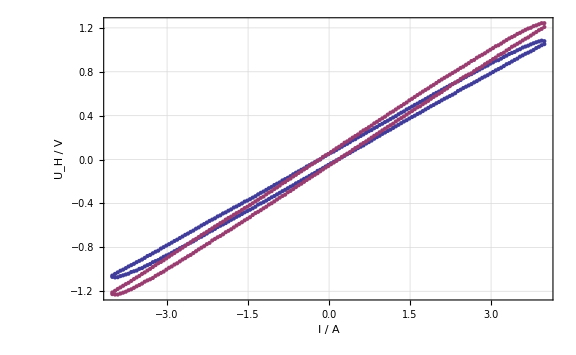

```mathematica
Show[
ListPlot[{datCali,datCaliCenter},PlotRange->All],
ImageSize->Large, FrameAndLines,
FrameLabel->{"I / A","U_H / V"}
]
```

```mathematica
firstHalf[dat_]:=dat⟦;;(Length[dat]/2),;;⟧
secondHalf[dat_]:=dat⟦(Length[dat]/2);;,;;⟧
caliDownCenter=Normal@LinearModelFit[Select[firstHalf@datCaliCenter,Abs[#⟦1⟧]≤2&],x,x]
caliUpCenter=Normal@LinearModelFit[Select[secondHalf@datCaliCenter,Abs[#⟦1⟧]≤2&],x,x]
caliDown=Normal@LinearModelFit[Select[firstHalf@datCali,Abs[#⟦1⟧]≤2&],x,x]
caliUp=Normal@LinearModelFit[Select[secondHalf@datCali,Abs[#⟦1⟧]≤2&],x,x]
useCali[dat_]:=({(caliDown/.x->#⟦1⟧),#⟦2⟧}&/@firstHalf@dat)~Join~
({(caliUp/.x->#⟦1⟧),#⟦2⟧}&/@secondHalf@dat);
```

0.0592133+0.321517 x

-0.0529237+0.32147 x

0.05147+0.280001 x

-0.0450854+0.280492 x

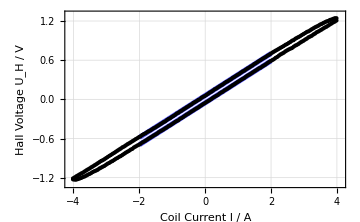
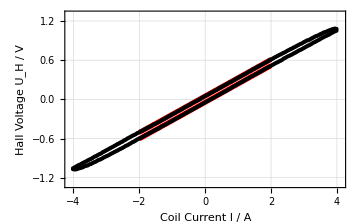

```mathematica
{Show[
Plot[{caliDownCenter,caliUpCenter},{x,-2,2},PlotStyle->Directive[Thickness[0.01],Lighter@Blue]],
ListPlot[{datCaliCenter},PlotRange->All,PlotStyle->Directive[Black,PointSize[Small]]],
ImageSize->Medium,FrameAndLines,
FrameLabel->{"Coil Current I / A","Hall Voltage U_H / V"}, PlotRange->{{-4.1,4.1},{-1.3,1.3}}
],
Show[
Plot[{caliDown,caliUp},{x,-2,2},PlotStyle->Directive[Thickness[0.01],Red]],
ListPlot[{datCali},PlotRange->All,PlotStyle->Directive[Black,PointSize[Small]]],
ImageSize->Medium,FrameAndLines,
FrameLabel->{"Coil Current I / A","Hall Voltage U_H / V"}, PlotRange->{{-4.1,4.1},{-1.3,1.3}}
]}
```

## anisotropy

{{-1.57354,0.0166079},{15.1376,0.545885}}

{{-2.08017,0.0153096},{5.86247,0.503212}}

1.25664×10^-6

Area: {44044.2,5277.62}

-1.57354+15.1376 x

-2.08017+5.86247 x

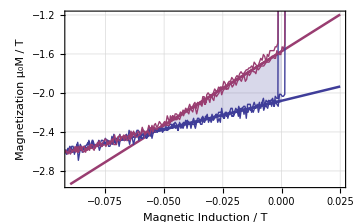
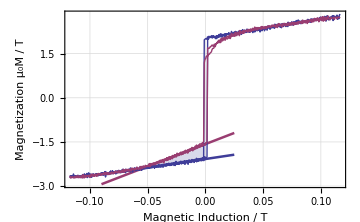

```mathematica
toErrorForm[a_]:={0.5*(a⟦1⟧+a⟦2⟧),0.5(a⟦2⟧-a⟦1⟧)};
reCali[{a_,b_}]:={a*0.1,(b-2.57066)*4.2/0.21364};
dataHard=useCali@datHard7;
dataEasy={#[[1]],#[[2]]*2.37/2.27+0.069}&/@(useCali@datEasy4);
dataHard=reCali/@dataHard;
dataEasy=reCali/@dataEasy;
v1=toErrorForm/@((upperFit=LinearModelFit[Select[dataHard,#⟦1⟧≤-0.005&&#⟦1⟧≥ -0.05&],x,x,ConfidenceLevel->.99])//#["ParameterConfidenceIntervals"]&)
v2=toErrorForm/@
((lowerFit=LinearModelFit[Select[dataEasy,#⟦1⟧≤-0.005&&#⟦1⟧≥ -0.05&],x,x,ConfidenceLevel->.99])//#["ParameterConfidenceIntervals"]&)
μ0=1.2566370614*10^-6
area[a1_,b1_,a2_,b2_]:=Integrate[a1-a2+(b1-b2)x,{x,(a1-a2)/(b2-b1),0}]*4/μ0
Print["Area: ",area~applyWithError~(v1~Join~v2)]
upperFit=Normal@upperFit
lowerFit=Normal@lowerFit
Show[
Plot[{lowerFit,upperFit},{x,-0.09,0.025},PlotStyle->Thickness[0.005]],
Plot[{lowerFit,upperFit},{x,-0.058,0},PlotStyle->Thickness[0.005],Filling->{1->{2}}],
ListLinePlot[{ dataEasy,dataHard}],
FrameAndLines,ImageSize->Medium,FrameLabel->{"Magnetic Induction / T","Magnetization μ_0M / T"},#
]&/@{{},{PlotRange->All}}
```

## drift

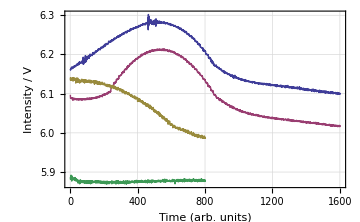

```mathematica
ListLinePlot[#⟦2⟧&/@#&/@{datDrift1,datDrift2,datDrift3,datDrift4},FrameAndLines,ImageSize->Medium,FrameLabel->{"Time (arb. units)","Intensity / V"}]
```

```mathematica
relVoltageError=0.2/6.2
```

0.0322581

```mathematica
absVoltageError=0.2
```

0.2

## kerr angle

```mathematica
(datKerr=Import["data\\kerrwinkelmessung.ods"]⟦1⟧⟦1;;18,3;;6⟧)//TableForm
datKerr=datKerr⟦2;;,;;⟧;
```

winkel in grad | I max | I min | Off-Set
301.333 | 0.235 | 0.005 | -2.015
301.833 | -0.478 | -0.663 | -2.015
302.333 | 0.112 | -0.028 | -0.891
302.833 | -0.274 | -0.369 | -0.891
303.333 | -0.504 | -0.554 | -0.891
303.833 | -0.562 | -0.568 | -0.891
304.333 | -0.457 | -0.419 | -0.891
304.833 | -0.202 | -0.119 | -0.891
305.333 | 0.22 | 0.346 | -0.891
305.833 | -0.156 | 0.016 | -1.879
306.333 | 0.584 | 0.801 | -1.879
306.833 | -0.272 | -0.016 | -3.647
307.333 | -0.312 | -0.013 | -4.76
307.833 | -0.331 | 0.008 | -6.019
308.333 | -0.348 | 0.029 | -7.529
308.833 | -0.545 | -0.116 | -9.208
308.833 | -0.5 | -0.071 | -9.208

```mathematica
calcC[a_,b_,off_]:=2(a-b)/(a+b-2off);
calcCAndErr[{angle_,a_,b_,off_}]:={angle,calcC[a,b,off],
Sqrt[(D[calcC[a,b,x],{x,1}]/.x->off)^2*(relVoltageError*(a+b-2off)/2)^2 + (D[calcC[x,b,off],{x,1}]/.x->a)^2*(0.00*a+0.001)^2+(D[calcC[a,x,off],{x,1}]/.x->b)^2*(b*0.00+0.001)^2]};
contrastsKerr=calcCAndErr/@datKerr;
(* α0 in this formula is the angle of maximum intensity, not of 0! *)
c[α_,I0_,I1_,α0_,ϕK_]:=(2(I1^2-I0^2)Sin[2(α-α0)*π/180]Sin[2ϕK*π/180])/(I0^2+I1^2+(I0^2-I1^2)Cos[2(α-α0)*π/180]Cos[2ϕK*π/180]);
toErrorForm/@((contrastFit=NonlinearModelFit[Select[contrastsKerr⟦1;; ,1;;2⟧,(#[[2]]>0&)],c[a,1,I1,a0,pK],{I1,{a0,214},{pK,-0.0001}},a,MaxIterations->1000,ConfidenceLevel->.99,VarianceEstimatorFunction->(1&),Weights->Select[contrastsKerr,#[[2]]>0&]⟦1;;,3⟧^(-2)])//#["ParameterConfidenceIntervals"]&)
toErrorForm/@((contrastFitLower=NonlinearModelFit[Select[contrastsKerr⟦1;; ,1;;2⟧,(#[[2]]<0&)],c[a,1,I1,a0,pK],{I1,{a0,214},{pK,-0.0001}},a,MaxIterations->1000,ConfidenceLevel->.99,VarianceEstimatorFunction->(1&),Weights->Select[contrastsKerr,#[[2]]<0&]⟦1;;,3⟧^(-2)])//#["ParameterConfidenceIntervals"]&)
contrastFit=Normal@contrastFit
contrastFitLower=Normal@contrastFitLower
```

{{-0.0170086,0.00419762},{213.887,0.0827766},{-0.0803747,0.0149187}}

{{-0.0192595,0.00276195},{213.839,0.17348},{-0.0624733,0.00510743}}

(0.00560958 Sin[1/90 (-213.887+a) π])/(1.00029+0.999707 Cos[1/90 (-213.887+a) π])

(0.00435984 Sin[1/90 (-213.839+a) π])/(1.00037+0.999627 Cos[1/90 (-213.839+a) π])

```mathematica
{0.5*(0.08037468850585706+0.06247333526629455),
1/2*Sqrt[0.014918676836340933^2+0.005107432216454513^2]}
{0.5*(0.017008636394335024+0.019259477516821846),1/2*Sqrt[0.004197616107371956^2+0.0027619498048192075^2]}
```

{0.071424,0.00788436}

{0.0181341,0.00251239}

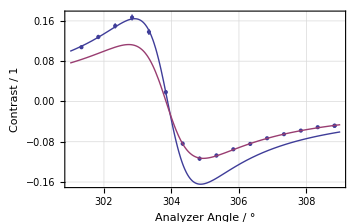

```mathematica
Show[
ErrorListPlot[contrastsKerr]
,Plot[{contrastFit,contrastFitLower},{a,301,309}],PlotRange->All,ImageSize->Medium,Axes->{True,False},AxesStyle->Thick,AxesOrigin->{0,0},FrameAndLines,FrameLabel->{"Analyzer Angle / °","Contrast / 1"}
]
```

## reflection angle dependence

```mathematica
(datAngleS=Import["data\\kerreinfallswinkelmessung.ods"]⟦1⟧⟦1;;13,2;;6⟧)//TableForm
datAngleS=datAngleS⟦2;;,;;⟧;
(datAngleP=Import["data\\kerreinfallswinkelmessungpp.ods"]⟦1⟧⟦1;;13,2;;6⟧)//TableForm
datAngleP=datAngleP⟦2;;,;;⟧;
```

winkel laser | winkel detektor | I max | I min | Off-Set
-45 | -5 | -0.008 | -0.114 | -2.907
-45 | 0 | -0.295 | -0.409 | -2.907
-45 | 5 | -0.146 | -0.278 | -2.907
-45 | 10 | -0.091 | -0.235 | -2.907
-45 | 15 | -0.257 | -0.404 | -2.907
-45 | 20 | -0.218 | -0.379 | -2.907
-45 | 25 | -0.132 | -0.305 | -2.907
-45 | 30 | -0.053 | -0.241 | -2.907
-45 | 35 | -0.027 | -0.226 | -2.907
-45 | 40 | -0.032 | -0.237 | -2.841
-45 | 45 | 0.142 | -0.083 | -2.841
-45 | 50 | -0.042 | -0.26 | -2.841

winkel laser | winkel detektor | I max | I min | Off-Set
-45 | -5 | -0.19 | -0.205 | -0.499
-45 | 0 | -0.111 | -0.143 | -0.499
-45 | 5 | -0.125 | -0.158 | -0.499
-45 | 10 | -0.119 | -0.154 | -0.499
-45 | 15 | -0.098 | -0.138 | -0.499
-45 | 20 | -0.078 | -0.122 | -0.499
-45 | 25 | -0.064 | -0.111 | -0.499
-45 | 30 | -0.11 | -0.144 | -0.499
-45 | 35 | -0.1 | -0.132 | -0.499
-45 | 40 | -0.074 | -0.109 | -0.499
-45 | 45 | -0.063 | -0.097 | -0.499
-45 | 50 | -0.024 | -0.063 | -0.499

{{-0.0121778,0.0278188},{0.00292582,0.00181988},{-0.0000204432,0.0000280076}}

-0.0121778+0.00292582 x-0.0000204432 x^2

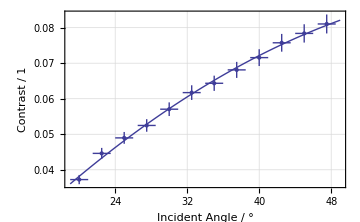
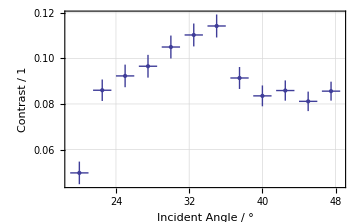

```mathematica
datAngleS2=calcCAndErr/@({0.5*(#⟦2⟧-#⟦1⟧),#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@datAngleS);
datAngleP2=calcCAndErr/@({0.5*(#⟦2⟧-#⟦1⟧),#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@datAngleP);
toErrorForm/@((fitAngleS=NonlinearModelFit[datAngleS2⟦1;;,1;;2⟧,a+b x+c x^2,{a,b,c},x,
ConfidenceLevel->.99,VarianceEstimatorFunction->(1&),Weights->datAngleS2⟦1;;,3⟧^(-2)])//#["ParameterConfidenceIntervals"]&)
fitAngleS=Normal@fitAngleS
{Show[
ErrorListPlot[{{#[[1]],#[[2]]},ErrorBar[1,#[[3]]]}&/@datAngleS2,
FrameAndLines,ImageSize->Medium,FrameLabel->{"Incident Angle / °","Contrast / 1"}
],
Plot[fitAngleS,{x,19,49}]
],
ErrorListPlot[{{#[[1]],#[[2]]},ErrorBar[1,#[[3]]]}&/@datAngleP2,
FrameAndLines,ImageSize->Medium,FrameLabel->{"Incident Angle / °","Contrast / 1"}
]}
```